# PHYS606 - PSET 1

## Question 1

### 1a

```mathematica
H1wa = {{0, -h Ω / 2}, {-h Ω/2, -h δ}};
evalsH1a = Eigenvalues[H1wa]
```

{1/2 h (-δ-√(δ^2+Ω^2)),1/2 h (-δ+√(δ^2+Ω^2))}

```mathematica
evecsH1a = Eigenvectors[H1wa]
```

{{-(δ-√(δ^2+Ω^2))/Ω,1},{-(δ+√(δ^2+Ω^2))/Ω,1}}

```mathematica
H1wa.{1, (δ - Sqrt[δ^2 + Ω^2])/Ω}
```

{-1/2 h (δ-√(δ^2+Ω^2)),-(h Ω)/2-(h δ (δ-√(δ^2+Ω^2)))/Ω}

```mathematica
flags = {h -> 1, Ω -> 1};

e[d_] := evalsH1a /. {h ->1, Ω->1, δ->d}
```

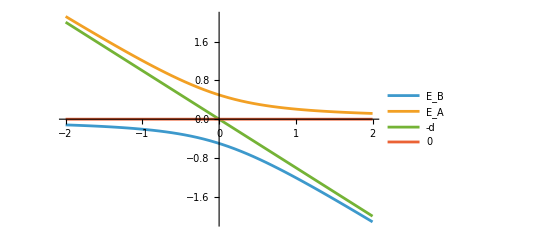

```mathematica
Plot[Evaluate[Append[e[d], {-d, 0}]], {d, -2, 2}, PlotLegends->{"E_B","E_A", "-d", "0"}]
```